## Formulations for Density Fluctuation-Dissipation Microscopic vs. Macroscopic

### Microscopic

Always at fixed temperature
T(∂n_i)/(∂μ) = ∑_j <n_i n_j>_c

Sum over j is over entire system, but only matters out to some length scale where density is correlated.

### Macroscopic

Just sum microscopic over the area/volume A. 
N ≡ ∑_j <n_j>
T∑_i (∂n_i)/(∂μ) = ∑_i ∑_j<n_i n_j>_c
T(∂N)/(∂μ) = <N^2> - <N>^2

The idea is that thermodynamic fluctuations do NOT go to 0 in the infinite system size, but relative fluctuations do.

#### Fluctuations in the Thermodynamic limit

Simple limits: 2D lattice, completely uncorrelated density fluctuations site to site, (but of course still correlated onsite) 
		<n_i n_i>_c = σ_n^2 on a given site.
	Microscopic relation is:
		T(∂n_i)/(∂μ) = ∑_j <n_i n_j>_c = σ_n^2 independent of system size. 
	Macroscopic relation is:
		T(∂N)/(∂μ) = Nσ_n^2
	Thermodnamic relative fluctuations do still go to 0:
		(< N^2 > - < N >^2)/(< N >^2) → σ_n^2/N
	Nothing surprising there.

### Mesoscopic (medium size)

Rough idea is that macroscopic formula still applies for a finite N in a finite box, even if  we can’t take advantage of the microscopic theory with translation invariance anymore. 

Measure both sides of this equation: T(∂N)/(∂μ) = <N^2> - <N>^2 and you’re done.

#### Experiments and theory

Trapped bulk gasses: 
		See: DOI: 10.1103/PhysRevLett.105.040401 and DOI: 10.1103/PhysRevLett.105.040402
		-Graphics--Graphics-
	Treat mesoscopic regions of gas as thermodynamic systems. 
	You need averaging box size to not have significant μ deviation? 
	You need box size > density correlation length? 
	You don’t need to single out and measure local vs. non-local correlations.
		Maybe we can’t say you need to measure non-local. Instead you can just use the mesoscopic reasoning. 
		
Fermions in a lattice (theory/simulation of principle) 
	DOI: 10.1103/PhysRevLett.106.225301 
		by Tin-Lun Ho for 2D Fermi-Hubbard on a lattice in 2011.  
	Theory estimation for how accurate thermometry would be b
	Simulate realizations of a real system with fluctuations, real trap, etc. 
	Sum all local and non-local correlations. Find slope, get temperature. 
	-Graphics--Graphics-

	Makes this mesocopic argument to use finite integration size (box averaging), or to use a Mott insulator where local is all there is. 
	
2 Other relevant experiments:
	DOI: 10.1103/PhysRevLett.96.130404
	 -Graphics-
	 
DOI: 10.1103/PhysRevA.81.031610 
-Graphics-

## Physical Systems and Limits to consider

#### Particles/Systems to consider

Bosons vs. Fermions
Infinite interactions vs. finite interactions 
0 Temperature vs. Infinite temperature

#### Observables

Local fluctuations
	For fermions, δn^2 = n - n^2 + 2d for doublon number d.
	For bosons, other things possible (more occupations). 
Isothermal compressibility
	dn/dμ for fixed temperature. 
	Fermions at 0 temperature this is just related to the density of states. 
	Bosons at 0 temperature I think is more complicated. 
Non-local fluctuations
	Not sure there’s an easy way to derive these: maybe from fluctuation dissipation relation?

#### Physics

Energy dispersion
	2D lattice  density of states is 2t ((1-Cos[kx a]) + (1-Cos[ky a])) where kx and ky are in ±π /a with spacing 2π/Nsites because it needs to be periodic with period Nsites. 
		1-Cos is just convenient so k=0 is 0 energy.
Density of states
	Same for both bosons and Fermions, but occupations are different. 
	Number of states with energy less than E* is 
Chemical potential as a function of density and temperature 
	Very different for Bosons and Fermions

#### Questions

Where does deBroglie wavelength come in?
	Fermions as T -> have linear density goes to 1/kF, density correlations should also stop at that length scale
	deBroglie wavelength (experimental correlations, not definition which goes as 1/T^1/2) smoothly connects to 1/kF at low temperatures. 
Quantum degeneracy should have finite compressibility for bosons, but Fermions -> 0, or just small?

### Density of states in a 2D Lattice

Fermi Surface for E = E*, using notation En = E*/4t  and kkx = kx*a
E* = 2t (2 - (Cos[kkx] + Cos[kky]))
2 En =2 - (Cos[kkx] + Cos[kky])
En goes from 0 to 2 at absolute maximum, but for now focus on En<1. 
Number of states per kk space area is Nsites^2/(2 π)^2. 
Just have to find the kk space area subject to these constraints.
Max kkx is when kky = 0, so Cos[kkxmax] = 1-2 En. 
Min kkx is when kky and kkx are both 0, and energy is 0, then Cos[kkx] is 1.
For a given kkx, kky goes from 0 up to kky* such that 2 (1-En) - Cos[kkx] = Cos[kky]

We want kkspace area = 4(∫^kkxmax)_0 dkkx (∫_0)^(kkymax given kkx = ArcCos[2-2En-Cos[kkx]])dkky 
= 4(∫^kkxmax)_0 dkkx ArcCos[2(1-En)-Cos[kkx]] 
Redefine gx = (1-Cos[kkx])/(2 En), 
	gx goes from 0 to 1 . 
	dgx *2 En/Sin[kkx] = dkkx 
	Cos[kkx] = 1- 2 gx En 
		Starts at 1 and goes to 1-2En 
		So 2 - 2En -Cos[kkx] goes from 1-2En to 1 
Then we can rewrite the integral as 
area= 8En(∫^1)_0 dgx ArcCos[2-2En-(1 - 2gx En)]/(√(1 - Cos[kkx]^2))
= 8En(∫^1)_0 dgx ArcCos[1-2En +2gx En]/(√(1 - (1- 2 gx En)^2))
= 8En(∫^1)_0 dgx ArcCos[1-2En(1- gx)]/(√(1 - (1- 2 gx En)^2))
Total number of states less than normalized  energy En is then 
Nstates= 8 Nsites^2/(2π)^2 En(∫^1)_0 dgx ArcCos[1-2En(1- gx)]/(√(1 - (1- 2 gx En)^2))
What is this integral? Well, En can be up to 1, and 1-2gx goes from 1 to -1. So numerator argument in principle goes from something negative to something positive, but always has magnitude less than 1. Will evaluate in a second.

```mathematica
(*Preliminary number of states *)8/(2π)^2 En NIntegrate[ArcCos[1 - 2En(1-gx)]/(√(1-(1 -2* gx En)^2)) ,{gx,0,1}] ;
```

NIntegrate::inumr: The integrand ArcCos[1-2 En (1-gx)]/(√(1-(1-2 En gx)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

One last detail: what about for 2>En > 1? Which can occur, it just isn’t taken into account by the math above.
	For En > 1 we still only have kkx, kky between -pi and pi. We just need to find the spectrum over again honestly. 
	What symmetries can we take advantage of?
		Look at distribution as a function of y such that E = 1 + y; 
		if I add pi to kkx and pi to kky, I get back 2 - the original distribution of energies in kkx and kky.
			y_(kkx, kky) = -y_(kkx+π, kky+π)
			so for each original y, i have a negative y in the shifted distribution. 
			This implies D_original[y] = D_shifted[-y]
			But shifting states around in kkx and kky space cannot do anything at all to the actual distribution of states. 
			So it has stayed the same. 
			But then D_original[y] = D_original[-y]
			D is symmetric about y=0, or E=1. 
	We can see that in the plots below:

```mathematica
Plot3D[{(2 - (Cos[kkx] + Cos[kky]))/2,(2 - (Cos[kkx+π] + Cos[kky+π]))/2,2-(2 - (Cos[kkx+π] + Cos[kky+π]))/2},{kkx,-π,π},{kky,-π,π}] (*Comparing spectrum with spectrum shifted by pi*)
Plot3D[{(2 - (Cos[(kkx+kky)/(√2)] + Cos[(kkx-kky)/(√2)]))/2},{kkx,-π,π},{kky,-π,π}] (*rotated *);
Plot3D[{D[(2 - (Cos[(kkxx+kky)/(√2)] + Cos[(kkxx-kky)/(√2)]))/2,kkxx] /. kkxx -> kkx},{kkx,-π,π},{kky,-π,π}] ;(*rotated derivative showing line of 0 derivative which is divergent density of states *)
```

-Graphics3D-

What this means for the density of states is that it is symmetric about En = 1.
	But the actual number of states less than En isn’t symmetric. Details. Not too important. Just means we have to be careful when defining the number of states using the symmetry property
		
Our math only works for E < 1 however, so let’s just piecewise it together to get the full  number of states, valid for E between 0 and 2
	If En < 1, just use En in formula.
	If En > 1, the number of states is (number at En = 1) + (number at En = 1)  - (number at En = 1- (En-1))
		number at En=1 is 0.5 nsites^2
	One way to do this is to add a Heaviside function to activate for En>1 that subtracts off 2x the function, and then adds 2x value at half filling = Nsites^2.

Another thing, let’s compare with density of states for free particle. As energy goes to 0, it should be basically the free particle dispersion, with a finite density of states.

2D free particle with energy 2t a^2 (kx^2 + ky^2 )/2 = ℏ^2 k^2/2m so with an effective mass = ℏ^2/2t a^2. Then density of states is what? Put the particles in a large finite periodic box of size Nsites*a -> k is still quantized, and periodic box means it is in units of 2π/(Nsites a) again. Also again positive and negative k are both allowed. 
	Number of states with energy less then E is (Nsites a)^2/(2π)^2 π kF^2 where kF^2 =2 m E /(ℏ^2) = E/ta^2 = 4 E/4t 1/a^2 = 4 En/a^2, plugging in for mass = ℏ^2/2t a^2. Therefore we get N(En) = Nsites^2/(2π)^2 4π En, then DN/DEn is Nsites^2/(2π)^2 4π

```mathematica
NaiveNumStates[En_,Nsites_] :=Nsites^2(8/(2π)^2(1-Abs[1-En]) NIntegrate[ArcCos[1 - 2(1-Abs[1-En])(1-gx)]/(√(1-(1 -2* gx (1-Abs[1-En]))^2)),{gx,0,1}] )
NumStates[En_,Nsites_] := NaiveNumStates[En,Nsites] + HeavisideTheta[En-1](Nsites^2 - 2 NaiveNumStates[En,Nsites])
NumStatesFreeParticle[En_,Nsites_] :=(4π)/(2π)^2 En* Nsites^2

(*Numerical derivative for density of states*)
ϵTest = 10^-10;
DenStates[EnTest_,Nsites_] := (NumStates[EnTest+ϵTest/2,Nsites]-NumStates[EnTest-ϵTest/2,Nsites])/ϵTest;
DenStatesFreeParticle[EnTest_,Nsites_] :=(NumStatesFreeParticle[EnTest+ϵTest/2,Nsites]-NumStatesFreeParticle[EnTest-ϵTest/2,Nsites])/ϵTest
```

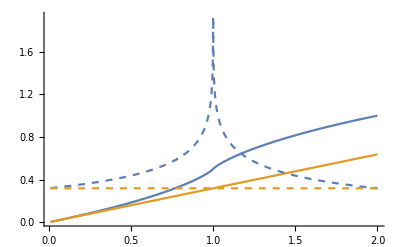

```mathematica
(*Plot some results*)
plt1 = Plot[{NumStates[EnTest,1],
 NumStatesFreeParticle[EnTest,1]},
{EnTest,0.01,2}, PlotRange -> All];
plt2 = Plot[{DenStates[EnTest,1],
 DenStatesFreeParticle[EnTest,1]},
{EnTest,0.01,2}, PlotStyle -> Dashed, PlotRange -> All];
Show[plt1,plt2]
```

### Non-interacting 2 component Fermions: Compressibility vs Density

Compressibility: 
	We don’t have to worry about local correlations at all. Just use macroscopic fluctuation dissipation. 
		Giant box, dn/dμ = 2*density of states at E = μ  for E[kx,ky]. Since we have 2 particles.
		We know the density for a given chemical potential, we know density of states for a given filling, so we know compressibility

Local fluctuations:
	Single species fermions has density n/2. Binomial statistics can have nothing other than p(1-p) as the variance in the density. 
	Now have two species, p^2is simply the probability of having both there at the same time. So the doublon occupancy is n^2/4.
	d is n^2/4 for non-interacting fermions
	locl fluctuations are then 2d + n - n^2 = 2^2d + 1^2s - (2d + (s))^2 = 2d + n - n^2 = n-n^2/2 for this system
	Important! This does NOT depend on temperature at all. It’s a property of the fact that these are independent binomial events.

Non-Local fluctuations:
	Derived below for a thermal gas, or for a lattice gas.
	Will directly do finite temperature, fixed mu first.

```mathematica
den[En_,Nsites_] :=2 NumStates[En,Nsites]/Nsites^2;
dndμ[En_,Nsites_] := 2DenStates[En, Nsites]
```

```mathematica
(*Make a table of dndμ vs density *)
EnLow = 0.01;
EnHigh = 2-EnLow;
EnSteps = 200;
EnDelta = (EnHigh -EnLow)/EnSteps;
datPlot = Table[{den[EnTest, 1],dndμ[EnTest, 1]},{EnTest,EnLow,EnHigh,EnDelta}];
```

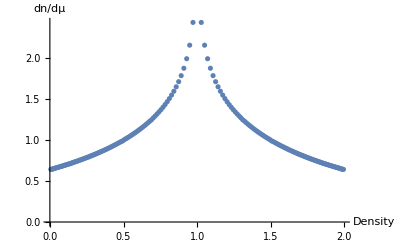

```mathematica
plt1 = ListPlot[datPlot , PlotRange -> All, AxesLabel -> {"Density", "dn/dμ"}]
```

### Deriving non - local fluctuations : 1D free particle first (warm up) Couldn’t get Finite Temperature analytics working well

Warm up with a free particle dispersion at some density. 
	Finite periodic box, with m_effchosen to be analogue to lattice. 
		
	Simplest way to get the ni nj fluctuations is to write out the operator for ni nj convert to k space then find expectation value. 
	Do 1D system first 
	Convention: a_x_1^† = 1/(√L)∑_k ⅇ^(ⅈ k x_1)a_k^†
	a_x_1^†a_x_1 a_x_2^†a_x_2= 1/L^2∑_(k_1, k_2, k_3, k_4) ⅇ^(ⅈ k_1 x_1)a_k_1^†ⅇ^(-ⅈ k_2 x_1)a_k_2 ⅇ^(ⅈ k_3 x_2)a_k_3^†ⅇ^(-ⅈ k_4 x_2)a_k_4 = 1/L^2∑_(k_1, k_2, k_3, k_4) ⅇ^(ⅈ (k_1 x_1- k_2 x_1+ k_3 x_2 -k_4 x_2))a_k_1^†a_k_2 a_k_3^†a_k_4  
	Various possibilities: 
		k_1 = k_2; k_3 = k_4 (k_3 = anything, including k_1); 
		k_1 ≠ k_2; k_1 = k_4; k_2 = k_3; 
	Stated again:
		k_1 = k_2= k_3 = k_4 ; 			Exponential: ⅇ^(ⅈ (k_1 x_1- k_2 x_1+ k_3 x_2 -k_4 x_2)) = 1				a_k_1^†a_k_2 a_k_3^†a_k_4 = a_k_1^†a_k_1 a_k_1^†a_k_1= a_k_1^†a_k_1
		k_1 = k_2; k_3 = k_4 (k_3 ≠ k_1); 	Exponential: ⅇ^(ⅈ (k_1 x_1- k_2 x_1+ k_3 x_2 -k_4 x_2)) = 1				a_k_1^†a_k_2 a_k_3^†a_k_4 = a_k_1^†a_k_1 a_k_3^†a_k_3 
		k_1 ≠ k_2; k_1 = k_4; k_2 = k_3; 	Exponential: ⅇ^(ⅈ (k_1 x_1- k_2 x_1+ k_3 x_2 -k_4 x_2)) =ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2)))	a_k_1^†a_k_2 a_k_3^†a_k_4 = a_k_1^†a_k_2 a_k_2^†a_k_1=a_k_1^†a_k_1-a_k_1^†a_k_1 a_k_2^†a_k_2 
	These are all possibilities. We sum over values of k_1, then over 1 of the other ones if necessary (k_3in first case, k_2 in second case) 
		Since we sum over k_1 and k_2 pairs twice, the exponential term becomes 2* the cosine in the end, the 1s become 2s. 
	Result:
		a_x_1^†a_x_1 a_x_2^†a_x_2= 1/L^2(∑_k_1 a_k_1^†a_k_1+ ∑_(k_1 ≠ k_2) a_k_1^†a_k_1 a_k_2^†a_k_2+ ∑_(k_1 ≠ k_2) ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2)))[a_k_1^†a_k_1-a_k_1^†a_k_1 a_k_2^†a_k_2] )
		First and second sum can be combined by letting sum over k_2and k_1run over all values independently, which becomes total N squared.
		Likewise for last sum with exponential, we can add on then subtract the term where k_2= k_1, since that’s actually 0.
		a_x_1^†a_x_1 a_x_2^†a_x_2= 1/L^2( ∑_(k_(1,) k_2) a_k_1^†a_k_1 a_k_2^†a_k_2+ ∑_(k_1,k_2) ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2)))[a_k_1^†a_k_1-a_k_1^†a_k_1 a_k_2^†a_k_2] )
		a_x_1^†a_x_1 a_x_2^†a_x_2= 1/L^2[∑_(k_1,k_2) ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2)))a_k_1^†a_k_1+ ∑_(k_(1,) k_2) a_k_1^†a_k_1 a_k_2^†a_k_2(1-ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2))))]
		To evaluate the first term, the sum over k_2is going to give 0 whenever x_1≠ x_2. 
			If it x_1 and x_2 are equal though, then the sum over k2 is just the number of sites, which is L (1D system for now)
				the term gives an extra factor of density, while the second term is 0. That’s the local fluctuations.
		a_x_1^†a_x_1 a_x_2^†a_x_2= δ_(x_(1,)x_2)∑_k_1 (a_k_1^†a_k_1)/L+ ∑_(k_(1,) k_2) (a_k_1^†a_k_1)/L(a_k_2^†a_k_2)/L(1-ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2))))
		a_x_1^†a_x_1 a_x_2^†a_x_2= δ_(x_(1,)x_2)a_x_1^†a_x_1+ ∑_(k_(1,) k_2) (a_k_1^†a_k_1)/L(a_k_2^†a_k_2)/L(1-ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2))))
	
	Ok, there’s the operator. What’s the expectation value in a thermal state?
		Let our system have inverse temp β and chemical potential μ, fermionic, with 1D dispersion for simplicity to start. 
		Density of states is what? Energy of a state is ℏ^2 k^2/2m = with an effective mass = ℏ^2/2t a^2 .
		As before,  kF^2 =2 m E /(ℏ^2) = E/ta^2 
		Number of states with energy less than En is (Nsites a)/(2π)2 kF (2 comes from + or -) = (Nsites a)/(2π)2  √(E/ta^2) =Nsites1/π √(E/t)  
		Density of states is Nsites1/(2π)√(1/(E t))  
		The thermal occupation of each state is 1/(1 + ⅇ^(β(E - μ))). 
		It’s actually easier to do as a sum over k rather than as a sum over E. The number of k states per 1D k space area is (Nsites a)/(2π)
		<a_x_1^†a_x_1 a_x_2^†a_x_2> = ∫dk_1 dk_2 (Nsites a)^2/(2π)^2 1/L^2 1/(1 + ⅇ^(β(t a^2 k_1^2 - μ)))1/(1 + ⅇ^(β(t a^2 k_2^2 - μ))) (1-ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2))))
		Transform to unitless k -> kk = k*a which ranges over real numbers, (x_1-x_2)/a -> m = an integer, all factors of lattice spacing a drop out
			kk1 and kk2 range from positive to negative, but integrand is even except for imaginary part, so ignore imaginary part. 
		<a_x_1^†a_x_1 a_x_2^†a_x_2> = 1/(2π)^2∫dkk_1 dkk_2  1/(1 + ⅇ^(β(t kk_1^2 - μ)))1/(1 + ⅇ^(β(t kk_2^2 - μ))) (1-Cos[(kk1-kk2)m])
		
		Also, average density is 
		<a_x_1^†a_x_1> = 1/(2π)∫dkk_1  1/(1 + ⅇ^(β(t kk_1^2 - μ)))
	
	Can we get analytic formulas for these? 
		
	Let’s plot the result for a few temperatures and μ, in units of t.

Plot some things for 0 temperature limit

Inverse Density is: 9.93459

Inverse Density is: 4.44288

Inverse Density is: 2.22144

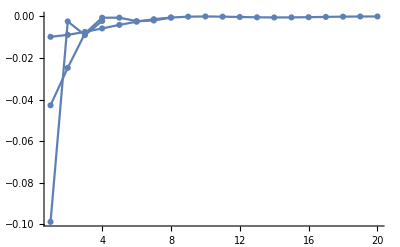

```mathematica
μTest = 0.1;
denTest = 2(√μTest)/(2π); (*this is 1/ Fermi wavelength, gotten from formula above*)

Print["Inverse Density is: ", N[1/denTest]];
mMax = 2*Round[1/denTest];
(*Plot connected correllator, so subtract off density squared *)
datListPlot = Table[{m,NIntegrate[1/(2π)^2(1-Cos[m(kk1-kk2)]), {kk1,-√μTest,√μTest}, {kk2,-√μTest,√μTest}] -denTest^2},{m,1,mMax,1}];
plt1 = ListPlot[datListPlot, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic];

μTest = 0.5;
denTest = 2(√μTest)/(2π); (*this is 1/ Fermi wavelength, gotten from formula above*)
Print["Inverse Density is: ", N[1/denTest]];
mMax = 2*Round[1/denTest];
(*Plot connected correllator, so subtract off density squared *)
datListPlot = Table[{m,NIntegrate[1/(2π)^2(1-Cos[m(kk1-kk2)]), {kk1,-√μTest,√μTest}, {kk2,-√μTest,√μTest}] -denTest^2},{m,1,mMax,1}];
plt2 = ListPlot[datListPlot, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic];

μTest = 2;
denTest = 2(√μTest)/(2π); (*this is 1/ Fermi wavelength, gotten from formula above*)
Print["Inverse Density is: ", N[1/denTest]];
mMax = 2*Round[1/denTest];
(*Plot connected correllator, so subtract off density squared *)
datListPlot = Table[{m,NIntegrate[1/(2π)^2(1-Cos[m(kk1-kk2)]), {kk1,-√μTest,√μTest}, {kk2,-√μTest,√μTest}] -denTest^2},{m,1,mMax,1}];
plt3 = ListPlot[datListPlot, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic];
Show[plt1, plt2, plt3, PlotRange -> All]
```

```mathematica
1/(2π)^2(1-Cos[m(kk1-kk2)])
```

(1-Cos[(kk1-kk2) m])/(4 π^2)

```mathematica
Print[N[denTest]]
```

0.450158

Analytic expression for 0 temperature:

```mathematica
Integrate[1/(2π)^2(1-Cos[m(kk1-kk2)]), {kk1,-√μ,√μ}, {kk2,-√μ,√μ}] -4 μ/(2π)^2
```

-μ/π^2+(μ-(Sin[m √μ] Sin[m √μ-2 π IntegerPart[(m √μ)/(2 π)]])/m^2)/π^2

```mathematica
dendenCorr1D0Temp[m_, den_] := -μ/π^2+(μ-(Sin[m √μ] Sin[m √μ-2 π IntegerPart[(m √μ)/(2 π)]])/m^2)/π^2 /. μ -> (π den)^2
(*Note you can't set density greater than 1 or result is unphysical...*)
```

Inverse Density is: 10.

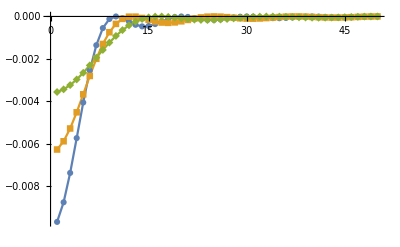

```mathematica
(*Plot connected correllator, so subtract off density squared *)
denTest = 0.1; (*this is 1/ Fermi wavelength, gotten from formula above*)
Print["Inverse Density is: ", N[1/denTest]];
mMax = 5*Round[1/denTest];
datListPlot1 = Table[{m,dendenCorr1D0Temp[m, denTest]},{m,1,mMax,1}];
datListPlot2 = Table[{m,dendenCorr1D0Temp[m, denTest*0.8]},{m,1,mMax,1}];
datListPlot3 = Table[{m,dendenCorr1D0Temp[m, denTest*0.6]},{m,1,mMax,1}];
ListPlot[{datListPlot1,datListPlot2,datListPlot3}, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic]
```

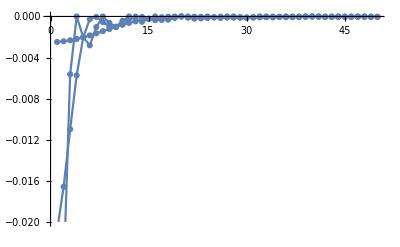

```mathematica
mMax = 50;
pltTable = Table[ 
ListPlot[Table[{m,dendenCorr1D0Temp[m, denTest]},{m,1,mMax,1}], PlotRange -> {{0, mMax},{-0.02,0.0}}, Joined -> True, PlotMarkers -> Automatic, PlotLegends-> denTesT],
{denTest, 0.05,0.3, 0.1}];
Show[Flatten[pltTable]]
```

Analytic expression for finite temperature?

```mathematica
(*And density*)
Integrate[1/(2π)1/(1 + Exp[β (kk1^2 - μ)]), {kk1,-∞, ∞},Assumptions->{β>0, μ > 0}]
```

-PolyLog[1/2,-ⅇ^(β μ)]/(2 √π √β)

```mathematica
(*Integrate[1/(2π)^2 1/(1 + Exp[β (kk1^2 - μ)])1/(1 + Exp[β (kk2^2 - μ)])(1-Cos[m(kk1-kk2)]), {kk1,-∞, ∞}, {kk2,-∞, ∞},Assumptions->{β>0, μ > 0}] *)
```

High temperature expression

```mathematica
Integrate[2 1/(2π)Exp[-β (kk1^2 - μ)], {kk1,0, ∞},Assumptions->{β>0, μ > 0}] 
Integrate[4 1/(2π)^2 Exp[-β (kk1^2 - μ)]Exp[-β (kk2^2 - μ)](1-Cos[m(kk1-kk2)]), {kk1,0, ∞}, {kk2,0, ∞},Assumptions->{β>0, μ > 0}]
```

ⅇ^(β μ)/(2 √π √β)

(ⅇ^(-m^2/(2 β)+2 β μ) ((-1+ⅇ^(m^2/(2 β))) √π-2 ⅇ^(m^2/(4 β)) DawsonF[m/(2 √β)] Erfi[m/(2 √β)]))/(4 π^(3/2) β)

```mathematica
dendenCorr1DFiniteTemp[m_,β_, μ_] :=(ⅇ^(-m^2/(2 β)+2 β μ) ((-1+ⅇ^(m^2/(2 β))) √π-2 ⅇ^(m^2/(4 β)) DawsonF[m/(2 √β)] Erfi[m/(2 √β)]))/(4 π^(3/2) β)- (ⅇ^(β μ)/(2 √π √β))^2
Series[dendenCorr1DFiniteTemp[m,β, μ], {m, ∞,2}]
```

ⅇ^(-m^2/(2 β)+2 β μ+O[1/m]^3) O[1/m]^3+(-ⅇ^(2 β μ)/(π^2 m^2)+O[1/m]^3)+ⅇ^(-m^2/(4 β)+2 β μ+O[1/m]^3) ((√(-1/β))/(π^(3/2) m)+O[1/m]^3)

Tail behavior is complicated... but maybe roughly is like 1/m^2 . Yes it is dominated by -ⅇ^(2 β μ)/(π^2 m^2)

Approx Inverse Density is: 1.8138

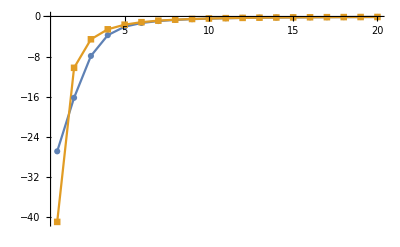

Approx Inverse Density is: 1.8138

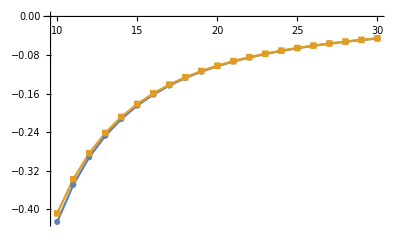

```mathematica
μTest = 3;
βTest = 1; (*high temp*)
denTestApprox = 2(√μTest)/(2π); (*this is 1/ Fermi wavelength, gotten from formula above*)

Print["Approx Inverse Density is: ", N[1/denTestApprox]];
mMax = 10*Round[1/denTestApprox];
mMin = 1; 
(*Plot connected correllator, so subtract off density squared *)
datListPlot = Table[{m,dendenCorr1DFiniteTemp[m,βTest, μTest]},{m,mMin,mMax,1}];
predListPlot = Table[{m,-ⅇ^(2 βTest μTest)/(π^2 m^2)},{m,mMin,mMax,1}];
plt1 = ListPlot[{datListPlot, predListPlot}, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic]

μTest = 3;
βTest = 1; (*high temp*)
denTestApprox = 2(√μTest)/(2π); (*this is 1/ Fermi wavelength, gotten from formula above*)

Print["Approx Inverse Density is: ", N[1/denTestApprox]];
mMax = 30;10*Round[1/denTestApprox];
mMin = 10; 
(*Plot connected correllator, so subtract off density squared *)
datListPlot = Table[{m,dendenCorr1DFiniteTemp[m,βTest, μTest]},{m,mMin,mMax,1}];
predListPlot = Table[{m,-ⅇ^(2 βTest μTest)/(π^2 m^2)},{m,mMin,mMax,1}];
plt1 = ListPlot[{datListPlot, predListPlot}, PlotRange -> All, Joined -> True, PlotMarkers -> Automatic]
```

Plan: Do fluctuations on a finite lattice in 2D with real energies. Analytics seem hopeless.

### 2D Lattice Fermi Gas - NonInteracting Numerical Simulations of Fluctuations

#### Plans

Do non-local fluctuations on a finite lattice in 2D with real energies, non-interacting. Analytics seem hopeless
	Finite temperature dependence included.  
	DOUBLE CHECK 2 COMPONENTS makes sense.
	See deBroglie wavelength crossover to 1/kF. 
	Find total fluctuations. 
Derive
	Use
		We have compressibility at 0 temperature.
		We have local fluctuations at any temperature. 
	Compressibility at finite temperature? 
	Check it matches in the limit as T -> 0

#### Calculations

What do we need:
	Define grid of k values
	Define energy of each k value
	Define thermal occupation of each k value
	Define operator
	Sum it all up. 

Conventions:
	Let k go from -π to π (meaning normalize out lattice spacing already.) 
	a_x_1^†a_x_1 a_x_2^†a_x_2= δ_(x_(1,)x_2)a_x_1^†a_x_1+ ∑_(k_(1,) k_2) (a_k_1^†a_k_1)/L^2(a_k_2^†a_k_2)/L^2(1-ⅇ^(ⅈ ((k_1 - k_2) (x_1-x_2))))
		Exponential is now really a vector dot product, with (kk1x, kk1y) - (kk2x, kk2y) dotted with the displacement. Displacement is number of latticer sites.
		Each operator is normalized by  2D area, not length now, which will get normalized out at the end of the summation. 
	Energ[kkx, kky] = (2 - (Cos[kkx] + Cos[kky]))/2 in units of 4 t. 
	number of states per k space area is Nsites^2/(2π)^2, but this doesn’t matter since I’m doing the discrete sum. 
	Occupancy of each state is 1/(1 + Exp[β (Energ[kkx,kky] - μ)])where β and μ are also measured in units of 4t. 
	Also have to subtract off the average density from the final value. 

Lastly, reasoning about what k vectors to use:
	(*If I have Nsites =4, that means I have 4 lattice sites in the entire system in either direction, and the box is 4 lattice sites long with N=5 same as N=1*)
	(*What k values exist then? k is periodic over whole cell 2p/L spacing between k values, but also is identical if we change by 2 pi /a since that produces the same wavefunction at each site.*)
	(*Therefore k goes from -pi/a to pi/a and if we have 4 sites, that means 4 value of k, so -pi/a, -pi/(2a), 0, pi/2a. Then rest is repeat.*)
	(*but we don’t want to sum over some values of k that singles out a certain direction? (Shouldnt’ matter in the end though...*)

#### Function and Analysis Setup

```mathematica
(*Global Functions to Generate Data*)
Nsites = 8; (*Use an even number, please*)
(*Other variables that should be cleared*)
Clear[β,μ, δvec,δvecY];
β;μ; δvec;δvecY;
(*2 element vector displacement in x and y*)

kTab =Flatten[ Table[{kkx, kky}, {kkx,-π,π-(2π)/Nsites, (2π)/Nsites},{kky,-π,π-(2π)/Nsites, (2π)/Nsites}],1];
	(*Careful! System is periodic, have to avoid overcounting edge lattice sites*)
numKs = Length[kTab] ; (*Should be Nsites squared*)
(*kTab is an array with each possible kk pairing.*)

(*Parameters of the model*)
Energ[kkx_,kky_] := (2 - (Cos[kkx] + Cos[kky]))/2
occup[kkx_,kky_, β_, μ_] := 1/(1 + Exp[β (Energ[kkx,kky] - μ)])
EnergTab =Flatten[ Table[Energ[kkx, kky], {kkx,-π,π, (2π)/(Nsites -1)},{kky,-π,π, (2π)/(Nsites -1)}],1];
occupTab =Flatten[ Table[occup[kkx, kky,β,μ], {kkx,-π,π, (2π)/(Nsites -1)},{kky,-π,π, (2π)/(Nsites -1)}],1];

(*Now compute the terms in the sum*)
toSumForCorrTab = Flatten[Table[
(*One table element for each possible pair of ii or jj in kTab*)
(*For each pair, construct the element =*)
1/Nsites^4 occupTab[[ii]]*occupTab[[jj]]*(1 - Cos[(kTab[[ii]]-kTab[[jj]]).{δvecX, δvecY}])
, {ii,1,numKs},{jj,1,numKs}],1];
toSumForDenTab = Table[
(*One table element for each possible pair of ii or jj in kTab*)
(*For each pair, construct the element =*)
1/Nsites^2 occupTab[[ii]]
, {ii,1,numKs}];
den2DFermi[ βVal_, μVal_]:= N[Total[toSumForDenTab]/. { β -> βVal, μ -> μVal}]
corr2DFermi[δXVal_, δYVal_, βVal_, μVal_]:= N[(Total[toSumForCorrTab] /. {δvecX -> δXVal,δvecY ->  δYVal, β -> βVal, μ -> μVal}) - den2DFermi[ βVal, μVal]^2]
```

```mathematica
(*Functions for Analysis*)
(*Generate full 2D connected density-density correlator array for a single species, including onsite fluctuations correctly accounted for*)
generate2DCorrArr[βval_, μval_, maxDist_] := Module[
{imgCorr, imgCorrPart}, 
(* suggested maximum distance is maxDistForimgCorr=Nsites/2 - 1; *) 
(*Calculate image correlator only on 1/4 of plane, then propagate to full to save computation *)
imgCorrPart = Table[corr2DFermi[ii,jj, βval,μval], {ii,0,maxDist},{jj,0,maxDist}];
imgCorr =Table[0, {ii,-maxDist,maxDist},{jj,-maxDist,maxDist}]; (*initialize then fill*)
For[ii=0, ii≤ maxDist, ii++, 
For[jj=0, jj≤ maxDist, jj++, 
(*ii and jj are real offset, matrices need some massaging to make that correct*)
imgCorr[[ii+maxDist+1]][[jj+maxDist+1]] = imgCorrPart[[ii+1]][[jj+1]] ;
imgCorr[[ii+maxDist+1]][[-jj+maxDist+1]] = imgCorrPart[[ii+1]][[jj+1]] ;
imgCorr[[-ii+maxDist+1]][[jj+maxDist+1]] =imgCorrPart[[ii+1]][[jj+1]] ;
imgCorr[[-ii+maxDist+1]][[-jj+maxDist+1]] =imgCorrPart[[ii+1]][[jj+1]] ;
]; 
]; 
(*Lastly, the central value is not correct. 
It needs to be calculated using an independent method assuming binomial statistics from the density. Onsite fluctuations are n *)
imgCorr[[maxDist+1,maxDist+1]] =den2DFermi[ βval, μval]- den2DFermi[ βval, μval]^2;
(*Return the 2D array at end*)
imgCorr
]

genRadData[imgCorrEx_] := (*Assumes imgCorr is a 2D array of size 2* something + 1*)
Module[{maxDist = Round[(Length[imgCorrEx]-1)/2], tabRet},
tabRet = Flatten[Table[{ √((ii)^2+ (jj)^2),imgCorrEx[[ii+maxDist+1]][[jj+maxDist+1]]}, {ii,0,maxDist},{jj,1,maxDist}],1];
(*Doesn't do the full 2D array, just a quadrant*)
tabRet
]

findDecayLength[dataSet_]:= (*Assumes dataSet is a list of xy pairs to be fit*)
Module[{a,λ},
model = a Exp[- r/λ]; 
fit = FindFit[dataSet, model,{λ, a},r];
{λ /. fit[[1]], a  /. fit[[2]]}
]

getCorrResultArr[imgCorrEx_, βval_,μval_]:= (*Returns a bunch of relevant data in a specific order*)
Module[{maxDist = Round[(Length[imgCorrEx]-1)/2], tabRet,
imgCorrNonlocOnly ,nonloccorrsSingleSpecies,loccorrsSingleSpecies,ϵTestd,
loccorrsd , nonloccorrsd,totcorrsd,totDensityd ,kappaFromCorrsd,kappaFromDerivd,λd,ad
},
(*Now sum the correlators and add the local fluctuations to get the compressibility*temperature.
For 2 component Fermi Gas, Local fluctuations should be (for n = total density =2 times single component density))
	2 component local fluctuations: n - n^2/2 because this is 4 d + 1s - (2d + 1s)^2 = 2d + n - n^2
	But single component fluctuations in terms of the total density are (n/2- (n/2)^2), and if we add these together we get n - n^2/2 as well. 
Nonlocal fluctuations for the 2 component gas a twice the nonlocal for a single component (defined here) *)
(*Correlators*)
imgCorrNonlocOnly = imgCorrEx; imgCorrNonlocOnly[[maxDist+1,maxDist+1]] = 0;
nonloccorrsSingleSpecies = Total[Flatten[imgCorrNonlocOnly]];
loccorrsSingleSpecies=imgCorrEx[[maxDist+1,maxDist+1]];
loccorrsd = 2*loccorrsSingleSpecies;
nonloccorrsd=2*nonloccorrsSingleSpecies; (*2 for both components*)
totcorrsd = loccorrsd + nonloccorrsd;
(*Density*)
totDensityd = 2*den2DFermi[ βval, μval];(*2 for both components*)
(*Kappa 2 ways *)
kappaFromCorrsd = βval*totcorrsd;
ϵTestd = 10^-10;
kappaFromDerivd = 2(den2DFermi[βval,μval+ϵTestd/2]-den2DFermi[βval,μval-ϵTestd/2])/ϵTestd;
(*Correlation lengths*)
{λd,ad} = findDecayLength[genRadData[imgCorrEx]];
tabRet = {βval, μval,loccorrsd , nonloccorrsd,totcorrsd,totDensityd ,kappaFromCorrsd,kappaFromDerivd,λd,ad};
tabRet
]
```

#### Single Run Analysis

β = 10 and μ = 0.4 resulting in: total density = 0.226239

Total Density-Density Correlator: 0.0715127 = Local: 0.200647 + non-local: -0.129134

Decay Length: 0.600159 sites and amplitude: -0.0431209

κ from Correlators: 0.715127 and κ from DOS: 0.715127 and fractional error: 1.69589×10^-7

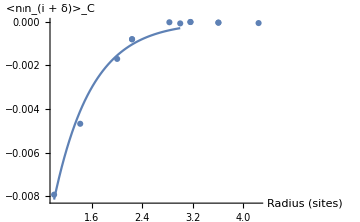
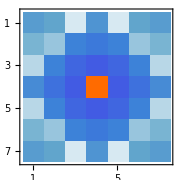
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Single Run Analysis*)
(*Set parameters and calculate*)
μTest =0.4;
βTest = 10;
maxDistForimgCorr=Nsites/2 - 1;

imgCorr = generate2DCorrArr[βTest, μTest,maxDistForimgCorr];
cRes =getCorrResultArr[imgCorr, βTest, μTest];

If[True,
(*Print some results*)
 (*{βval, μval,loccorrsd , nonloccorrsd,totcorrsd,totDensityd ,kappaFromCorrsd,kappaFromDerivd,λd,ad}*)
Print["β = ", cRes[[1]], " and μ = ", cRes[[2]], " resulting in: total density = ", cRes[[6]]]
Print["Total Density-Density Correlator: ", cRes[[5]], " = Local: ", cRes[[3]], " + " , "non-local: ", cRes[[4]]]
Print["Decay Length: ", cRes[[9]], " sites and amplitude: ", cRes[[10]]]
Print["κ from Correlators: ",cRes[[7]], " and κ from DOS: ", cRes[[8]], " and fractional error: ", Abs[cRes[[8]]-cRes[[7]]]/Abs[(cRes[[8]]+cRes[[7]])/2] ] ;
];

(*Plot some results*)
plt1 = ListPlot[genRadData[imgCorr], PlotMarkers -> Automatic,AxesLabel -> {"Radius (sites)","<n_in_(i + δ)>_C"}];
λshow = findDecayLength[genRadData[imgCorr]][[1]];ashow = findDecayLength[genRadData[imgCorr]][[2]];
plt2= Plot[(ashow *Exp[-r/λshow]),{r,1,maxDistForimgCorr}];
plt3 = Plot[{2*den2DFermi[ βTest, μVal],2*NumStates[μVal,1]}, {μVal,0,2},PlotLabels->{"Real density in box", "Thermodynamic density"}, AxesLabel -> {"μ (units of 4t)","Density"}]; (*Factor of 2 for 2 components*)
plt4 = MatrixPlot[imgCorr];
{Show[plt1,plt2, PlotRange -> All, ImageSize -> Medium], Show[plt3, ImageSize -> Medium], Show[plt4, ImageSize -> Small]}
```

#### Multi Run Analysis - vs. μ

```mathematica
(*Multi-Run Analysis*)
(*Set parameters and calculate*)
βTest = 4;
maxDistForimgCorr=Nsites/2 - 1;
debugPrintTiming=False;
(*Set array of μ values to iterate over, and arrays to save data in*)
 μLow = 0.0;
μHigh = 2;
μNum = 20;
(*For now, fix β and only iterate over μ*)

(*Initialize dependent arrays*)
μDel =(μHigh - μLow)/(μNum -1);
μTestArr = Table[μval, {μval, μLow, μHigh,μDel}];
cResArr = {}; (*Will append each datset to this*)

(*Iterate through and get the data*)
For[μInd =1, μInd ≤ μNum, μInd++, 
(*Initialize changing variables*)
μTest = μTestArr[[μInd]];

(*Get the data *)
imgCorr = generate2DCorrArr[βTest, μTest,maxDistForimgCorr];
cRes = getCorrResultArr[imgCorr, βTest, μTest];
cResArr = Append[cResArr,cRes];

(*Print timing for debugging*)
If[debugPrintTiming,
Print["Finished calculation for μ of: ",μTest, " at ", TimeObject[]];
];
];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Vs μ, with β = 4

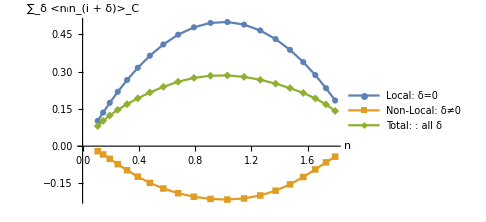
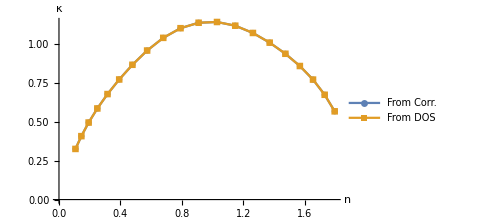
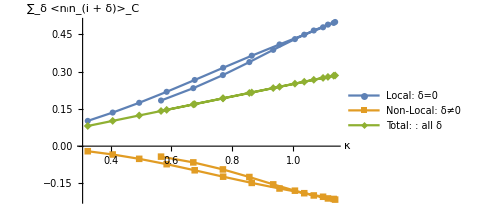
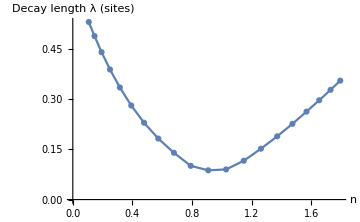

```mathematica
(*Analyze Multi-Run Analysis*)
(*Now extract data to make nice plots from cResArr*)
(*Use these indices to select which data arrays to plot *)
βInd = 1;μInd =2;locCorrInd=3;nlCorrInd=4;totCorrInd=5;denInd = 6;κCorrInd = 7;κDOSInd = 8;λInd = 9;aInd = 10;
genListPlotData[xInd_, yInd_,cResArrEx_] := Module[{},{cResArrExᵀ[[xInd]],cResArrExᵀ[[yInd]]}ᵀ] (*x ind is indices for x axis, y is for y data*)

Print["Vs μ, with β = ", βTest]
pltκvsn= ListPlot[{genListPlotData[denInd, κCorrInd,cResArr],genListPlotData[denInd, κDOSInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic, 
PlotLegends -> {"From Corr.", "From DOS"}, AxesLabel->{"n","κ"}];
pltλvsn= ListPlot[{genListPlotData[denInd, λInd,cResArr]}, 
Joined -> True, PlotMarkers -> Automatic,
AxesLabel->{"n","Decay length λ (sites)"}];
pltCorrsvsn= ListPlot[{genListPlotData[denInd, locCorrInd,cResArr],genListPlotData[denInd, nlCorrInd,cResArr],genListPlotData[denInd, totCorrInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic,
PlotLegends -> {"Local: δ=0", "Non-Local: δ≠0", "Total: : all δ"}, AxesLabel->{"n","∑_δ <n_in_(i + δ)>_C"}];
pltCorrvsκ= ListPlot[{genListPlotData[κCorrInd, locCorrInd,cResArr],genListPlotData[κCorrInd, nlCorrInd,cResArr],genListPlotData[κCorrInd, totCorrInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic,
PlotLegends -> {"Local: δ=0", "Non-Local: δ≠0", "Total: : all δ"}, AxesLabel->{"κ","∑_δ <n_in_(i + δ)>_C"}];
imgSizeToShow = Medium;
{Show[pltCorrsvsn, ImageSize ->imgSizeToShow ],Show[pltκvsn, ImageSize -> imgSizeToShow ],Show[pltCorrvsκ, ImageSize -> imgSizeToShow ], Show[pltλvsn, ImageSize -> imgSizeToShow ]}
```

#### Multi Run Analysis - vs. β

```mathematica
(*Multi-Run Analysis*)
(*Set parameters and calculate*)
μTest = 0.88;
maxDistForimgCorr=Nsites/2 - 1;
debugPrintTiming=False;
(*Set array of μ values to iterate over, and arrays to save data in*)
 βLow = 0.1;
βMid = 8;
βHigh = 100;
βNum = 30;
βNumLowMid = 15;
βNumMidHigh = βNum - βNumLowMid;

(*Initialize dependent arrays. For β, we want to have enough datapoints at both low and high temperatures*)
βDelLowMid =(βMid - βLow)/(βNumLowMid-1);
βDelMidHigh =(βHigh- βMid)/(βNumMidHigh-1);
βTestArrLowMid = Table[βval, {βval,βLow, βMid,βDelLowMid}];
βTestArrMidHigh= Table[βval, {βval,βMid, βHigh,βDelMidHigh}];
βTestArr = Join[βTestArrLowMid,βTestArrMidHigh];
cResArr = {}; (*Will append each datset to this*)

(*Iterate through and get the data*)
For[βInd =1, βInd ≤ βNum, βInd++, 
(*Initialize changing variables*)
βTest = βTestArr[[βInd]];

(*Get the data *)
imgCorr = generate2DCorrArr[βTest, μTest,maxDistForimgCorr];
cRes = getCorrResultArr[imgCorr, βTest, μTest];
cResArr = Append[cResArr,cRes];

(*Print timing for debugging*)
If[debugPrintTiming,
Print["Finished calculation for β of: ",βTest, " at ", TimeObject[]];
];
];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

Vs β, with μ = 0.88

Plot vs. T

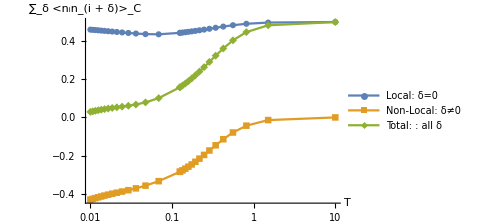
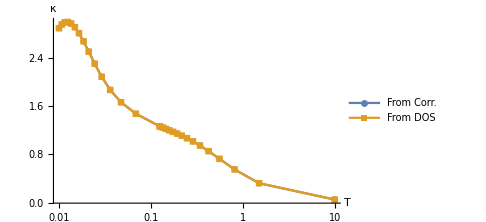
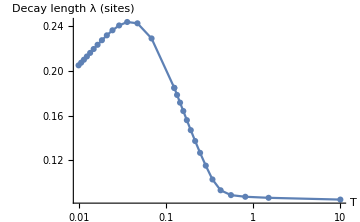
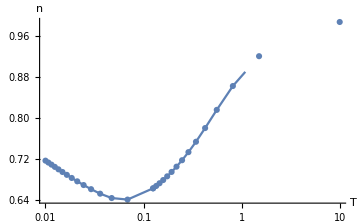

Plot vs. β

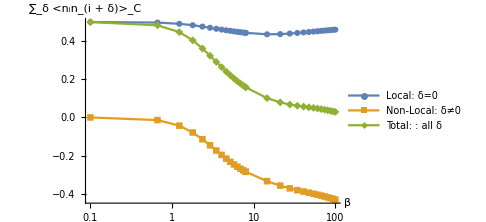
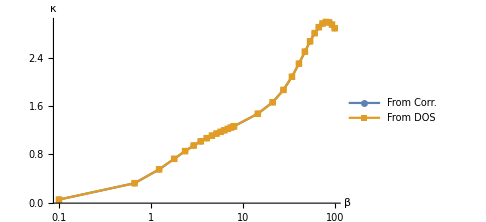
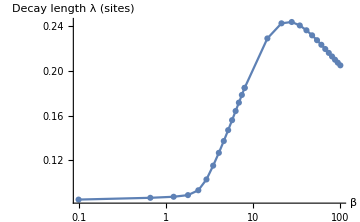

```mathematica
(*Analyze Multi-Run Analysis*)
(*Now extract data to make nice plots from cResArr*)
(*Use these indices to select which data arrays to plot *)
βInd = 1;μInd =2;locCorrInd=3;nlCorrInd=4;totCorrInd=5;denInd = 6;κCorrInd = 7;κDOSInd = 8;λInd = 9;aInd = 10;
genListPlotData[xInd_, yInd_,cResArrEx_] := Module[{},{cResArrExᵀ[[xInd]],cResArrExᵀ[[yInd]]}ᵀ] (*x ind is indices for x axis, y is for y data*)
genListPlotDataInvXInd[xInd_, yInd_,cResArrEx_] := Module[{},{1/cResArrExᵀ[[xInd]],cResArrExᵀ[[yInd]]}ᵀ] (*x ind is indices for x axis, y is for y data*)

Print["Vs β, with μ = ", μTest]
Print["Plot vs. T"];
pltκvsT=  ListLogLinearPlot[{genListPlotDataInvXInd[βInd, κCorrInd,cResArr],genListPlotDataInvXInd[βInd, κDOSInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic, 
PlotLegends -> {"From Corr.", "From DOS"}, AxesLabel->{"T","κ"}];
pltλvsT= ListLogLinearPlot[{genListPlotDataInvXInd[βInd, λInd,cResArr]}, 
Joined -> True, PlotMarkers -> Automatic,
AxesLabel->{"T","Decay length λ (sites)"}];
pltCorrsvsT=  ListLogLinearPlot[{genListPlotDataInvXInd[βInd, locCorrInd,cResArr],genListPlotDataInvXInd[βInd, nlCorrInd,cResArr],genListPlotDataInvXInd[βInd, totCorrInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic,
PlotLegends -> {"Local: δ=0", "Non-Local: δ≠0", "Total: : all δ"}, AxesLabel->{"T","∑_δ <n_in_(i + δ)>_C"}];
pltnvsT=  ListLogLinearPlot[{genListPlotDataInvXInd[βInd, denInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic,
AxesLabel->{"T","n"}];
imgSizeToShow = Medium;
{Show[pltCorrsvsT, ImageSize ->imgSizeToShow, PlotRange -> All ],
Show[pltκvsT, ImageSize -> imgSizeToShow , PlotRange -> All],
Show[pltλvsT, ImageSize -> imgSizeToShow , PlotRange -> All],
Show[pltnvsT, ImageSize -> imgSizeToShow , PlotRange -> All]}

Print["Plot vs. β"];
pltκvsβ=  ListLogLinearPlot[{genListPlotData[βInd, κCorrInd,cResArr],genListPlotData[βInd, κDOSInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic, 
PlotLegends -> {"From Corr.", "From DOS"}, AxesLabel->{"β","κ"}];
pltλvsβ= ListLogLinearPlot[{genListPlotData[βInd, λInd,cResArr]}, 
Joined -> True, PlotMarkers -> Automatic,
AxesLabel->{"β","Decay length λ (sites)"}];
pltCorrsvsβ=  ListLogLinearPlot[{genListPlotData[βInd, locCorrInd,cResArr],genListPlotData[βInd, nlCorrInd,cResArr],genListPlotData[βInd, totCorrInd,cResArr]},
Joined -> True, PlotMarkers -> Automatic,
PlotLegends -> {"Local: δ=0", "Non-Local: δ≠0", "Total: : all δ"}, AxesLabel->{"β","∑_δ <n_in_(i + δ)>_C"}];
imgSizeToShow = Medium;
{Show[pltCorrsvsβ, ImageSize ->imgSizeToShow, PlotRange -> All ],
Show[pltκvsβ, ImageSize -> imgSizeToShow , PlotRange -> All],
Show[pltλvsβ, ImageSize -> imgSizeToShow , PlotRange -> All]}
```

#### Plans

Looking for: 
	deBroglie wavelength behavior at high temperature, going over to 1/kF at low temperature? 
	non-local fluctuations go to 0 at high temperature
		Do they go to 0 like 1/debroglie wavelength^2? Seems like, by definition, they will. Saturate at kF^2 at low temp?
	Overall behavior of kappa in the low and high temperature limit
		High should go like β (for small beta), low should ultimately match thermodynamic limit derivation?
			Low temp (high beta) will not work because of discrete density of states.

#### Older stuff

If we want a density of 0.8 for example, at 0 temperature, what μVal to use? 
Have to use enough lattice sites for thermodynamic density formula to be correct.

```mathematica
NumStates[0.893356,1]*2
μForDenEq0p8At0Temp = 0.893356;
```

0.8

```mathematica
(*Some other visualization*)
ContourPlot[occup[kkx,kky, 100, 1],{kkx,-π,π},{kky,-π,π}];
δvecXTest = 4;
δvecYTest = 2;
ContourPlot[occup[kkx,kky, 100, 1](1 - Cos[({kkx,kky}).{δvecXTest, δvecYTest}]), {kkx,-π,π},{kky,-π,π}];
```